```mathematica
ClearAll["Global`*"]
```

This is a collection of notes on the Cornish-Fisher (CF) expansion and its utility in quantile regression studies. 
The CF expansion [1] aims in approximating general distributions as deviates of the normal distribution. Given a distribution with mean, variance, skewness and kurtosis , CF allows to estimate the quantile  at probability level  as a deviation from the known, correspondent quantile  of a standard normal (i.e., gaussian with zero mean and unit variance) as:

                       (1)

For details on this formalism and useful literature on the CF expansion and quantile regression we refer the reader to: https://arxiv.org/abs/2211.04608

 are considered as skewness and kurtosis parameters. Their relation to the sample skewness and kurtosis is described in [2] (and also mentioned in [3]). In the case of small skewness and kurtosis such parameters and their true value are equal. In our paper we work in that limit. 
Additionally, here we present few examples considering Eq. (1) and show that even for small values  we can still observe good results. Few additional points on this can be found in the preprint https://arxiv.org/abs/2211.04608

[1] E. A. Cornish and R. A. Fisher. Moments and Cumulants in the Specification of Distributions. Revue De
L’Institut International De Statistique / Review of the International Statistical Institute, 5(4):307–320,
1937. doi: https://doi.org/10.2307/1400905.

[2] D. Maillard. A user’s guide to the Cornish–Fisher expansion. Available at SSRN 1997178. 2012.
[3] C.-O. Amédée-Manesme, F. Barthélémy, and D. Maillard. Computation of the corrected Cornish–Fisher expansion using the
response surface methodology: application to VaR and CVaR. Ann Oper Res, 281:423–453, 2019. doi: https://doi.org/10.1007/s10479-018-2792-4.

Contents

- Testing Cornish-Fisher Expansion (1937)	

	- Cornish-Fisher Expansion (1937)
	- Tests on Beta distribution
	
- Linking changes in quantiles to changes in statistical moments

	- Derivatives
	- Derivatives in the neighborhood of a standard normal
	- Orthogonality

- From a quantile function to a PDF

	- Standard normal
	- Shift in the mean
	- Shift in variance
	- Shift in skewness 
	- Shift in kurtosis

### Testing Cornish-Fisher Expansions (1937)

#### Cornish-Fisher Expansions (1937)

```mathematica
(*Cornish-Fisher Expansion (1937)*)
(*
Input.
μ -> mean;
  v -> variance;
  γ -> skewness;
  κ -> kurtosis;
  p -> probability level (e.g., 0.95);
Output: the p quantile of the distribution.
*)
CF[μ_,v_,γ_,κ_,p_]:=
Module[
{zp,w,yp,σ,k},
(*Define the excess kurtosis*)
k=κ-3;
zp=Quantile[NormalDistribution[0,1],p];
w=zp+((zp^2)-1)(γ/6)+((zp^3)-3zp)(k/24)-(2(zp^3)-5zp)((γ^2)/36);
(*Define the standard deviation*)
σ=Sqrt[v];
yp=μ+σ*w;
yp
]
```

#### Tests on Beta distribution

In the case of Gaussian distribution the CF expansion is exact. So, no need to try it out for Gaussians.

Here we focus on the case of a (stationary) Beta distribution with non-zero skewness and kurtosis. For the Beta distribution, Mathematica can compute the exact quantile, therefore providing a useful ground truth to test our estimator.

We consider two cases:

(a) we estimate the 0.95 quantile via the quantile function (Ground truth) and the CF expansion

(b) we estimate all quantiles at  every dp = 0.01 via the quantile function (Ground truth) and the CF expansion

```mathematica
(*For this example we choose the parameters as α = 2 and β = 4*)
(*α=3;
β=8;*)
α=2;
β=12;
(*Mean*)
m=Mean[BetaDistribution[α,β]];
(*Variance*)
v=Variance[BetaDistribution[α,β]];
(*Skewness*)
s=Skewness[BetaDistribution[α,β]];
(*Kurtosis*)
k=Kurtosis[BetaDistribution[α,β]];
```

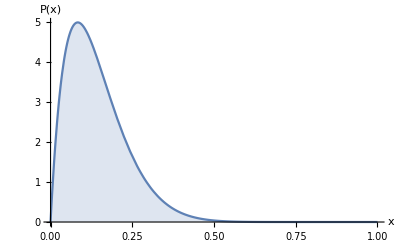

```mathematica
Plot[PDF[BetaDistribution[α,β],x],{x,0,1},PlotRange->All,
FrameTicks->Automatic,FrameTicksStyle->Directive[Black,12],Filling->Bottom,AxesLabel->{x,P[x]},LabelStyle->Directive[Black,16]]
```

TEST (a)

We compute the 0.95 quantile using the quantile function (i.e., ground truth) and the CF expansion.

```mathematica
(*Let's compute the 0.95 quantile. We do so in two ways: (a) using the quantile function of the Beta distribution (i.e., this gives us the exact value); (b) using the CF expansion*)

p=0.95;
Print[{"Mean,variance,skewness,kurtosis"}]
Print[{m,v,s,k}//N]
(*E.g., q = 0.95*)
Print[StringJoin["The value of the quantile q = ",ToString[p]," is ",ToString[Quantile[BetaDistribution[α,β],p]]]]
Print[StringJoin["Approximation given by Cornish-Fisher expansion is ",ToString[CF[m,v,s,k,p]]]]
```

{Mean,variance,skewness,kurtosis}

{0.142857,0.00816327,0.988212,4.02574}

The value of the quantile q = 0.95 is 0.31634

Approximation given by Cornish-Fisher expansion is 0.313324

TEST (b)

We compute the all quantiles from p = 0.01 to p = 0.99 every dp = 0.0001 using the quantile function (i.e., ground truth) and the CF expansion.

```mathematica
groundTruth=Table[{p,Quantile[BetaDistribution[α,β],p]},{p,0.05,0.95,0.0001}];
cfExpansion=Table[{p,CF[m,v,s,k,p]},{p,0.05,0.95,0.0001}];
gaussian=Table[{p,Quantile[NormalDistribution[m,Sqrt[v]],p]},{p,0.05,0.95,0.0001}];
```

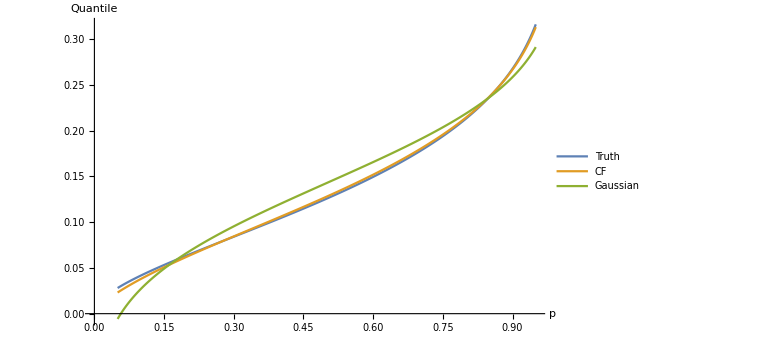

```mathematica
ListLinePlot[{groundTruth,cfExpansion,gaussian},PlotLegends->{"Truth","CF","Gaussian"},AxesLabel->{"p","Quantile"},LabelStyle->Directive[Black,16], ImageSize->Large]
```

Notice that this expansion is not anymore valid for larger and larger skewness and kurtosis values. In the case above, where skewness ~ 1 and (excess) kurtosis ~ 1, the expansion is already strictly not valid and corrections should be added to the skewness and kurtosis, as described in https://papers.ssrn.com/sol3/papers.cfm?abstract_id=1997178 .

Nonetheless, reasonably good results can still be achieved as shown in the plot above.

### Linking changes in quantiles to changes in statistical moments

In https://arxiv.org/pdf/2211.04608.pdf we are interested in defining a single framework to study changes in both quantiles and moments of a distribution from time series data. Linear trends in quantiles can be computed using quantile regression. We then quantify how independent shifts in moments of the distribution can explain the observed changes in quantiles. 

To read this paragraph, the reader should be familiar with the derivation shown in Section 3.2 of https://arxiv.org/pdf/2211.04608.pdf . Here we just show (compute) the important steps: 

(a) derivatives of the Cornish-Fisher distribution in terms of the mean, variance, skewness and kurtosis; 
(b) estimation of those derivatives in the neighborhood of a standard normal;
(c) orthogonality of the derived polynomials
(d) plotting the derived polynomials

#### Derivatives

```mathematica
(*Clear the environment*)
ClearAll["Global`*"]
```

```mathematica
(*Cornish-Fisher Expansion (1937)*)
(*
μ -> mean;
v -> variance;
γ -> skewness;
κ -> kurtosis.
*)
(*For now, we consider z, the quantile function of a standard normal, as just an other variable and we do not evaluate it.*)
CFexpansion[μ_,v_,γ_,κ_,z_]:=
μ+Sqrt[v]*( z+((z^2)-1)(γ/6)+((z^3)-3z)(κ/24)-(2(z^3)-5z)((γ^2)/36))
```

```mathematica
expansion=CFexpansion[μ,v,γ,κ,z]
```

√v (z+1/6 (-1+z^2) γ-1/36 (-5 z+2 z^3) γ^2+1/24 (-3 z+z^3) κ)+μ

Changes in the mean

```mathematica
changesMean=D[expansion,μ]
```

1

Changes in the variance

```mathematica
changesVariance=D[expansion,v]
```

(z+1/6 (-1+z^2) γ-1/36 (-5 z+2 z^3) γ^2+1/24 (-3 z+z^3) κ)/(2 √v)

Changes in the skewness

```mathematica
changesSkewness=D[expansion,γ]
```

√v (1/6 (-1+z^2)-1/18 (-5 z+2 z^3) γ)

Changes in the kurtosis

```mathematica
changesKurtosis=D[expansion,κ]
```

1/24 √v (-3 z+z^3)

#### Derivatives in the neighborhood of a standard normal

A standard normal is a Gaussian distribution with mean and variance equal to 0 and 1 respectively. Skewness and (excess) kurtosis are also zero. In the “moment space” studied here is then represented by the point (μ = 0, v = 1, γ = 0, κ = 0). We evaluate the derivatives computed in the step above in this point.

This step allows us to defined the 4 polynomials as in Eq. (8) in https://arxiv.org/pdf/2211.04608.pdf 
Below we also evaluate z as the quantile function of a standard normal.

```mathematica
polynomials={changesMean,changesVariance,changesSkewness,changesKurtosis}/.{μ->0,v->1,γ->0,κ->0,z->Quantile[NormalDistribution[0,1],p]}
```

{1,ConditionalExpression[-InverseErfc[2 p]/(√2), 0≤p≤1],ConditionalExpression[1/6 (-1+2 InverseErfc[2 p]^2), 0≤p≤1],ConditionalExpression[1/24 (3 √2 InverseErfc[2 p]-2 √2 InverseErfc[2 p]^3), 0≤p≤1]}

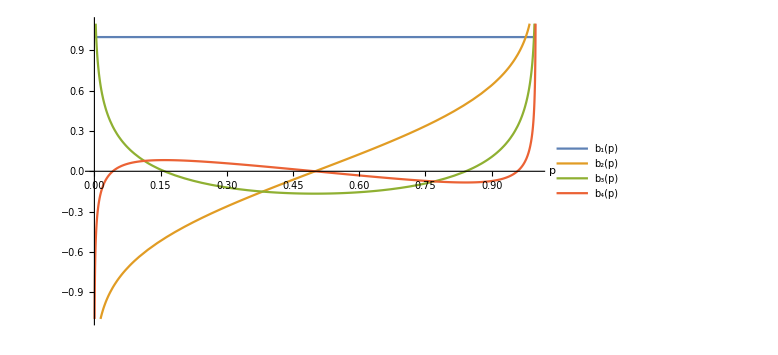

```mathematica
Plot[{polynomials[[1]],polynomials[[2]],polynomials[[3]],polynomials[[4]]},{p,0,1},PlotRange->{-1.1,1.1},FrameTicks->Automatic,FrameTicksStyle->Directive[Black,12],AxesLabel->{p},LabelStyle->Directive[Black,12],ImageSize->Large,PlotLegends->{"b_1(p)","b_2(p)","b_3(p)","b_4(p)"}]
```

#### Orthogonality

These polynomials are Hermite polynomials of the quantile function  of a standard normal. They are orthogonal in .

```mathematica
norms=
Table[
Table[
Integrate[Evaluate[polynomials[[i]]*polynomials[[j]]],
{p,0,1}],
{j,1,4}],{i,1,4}]
```

{{1,0,0,0},{0,1/4,0,0},{0,0,1/18,0},{0,0,0,1/96}}

```mathematica
norms//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1/4 | 0 | 0
0 | 0 | 1/18 | 0
0 | 0 | 0 | 1/96)

### From a Quantile function to PDF

The polynomials derived (or better, derived by Cornish and Fisher) in the above sections tell us how the quantile function of a distribution changes when we perturbed it in the direction of the first four moments.  Here we want to visualize these changes in terms of the PDF. In other words we are interested in the opposite process: given a new, perturbed quantile function, how is the PDF going to change?

For simplicity here we refer to mean, variance, skewness and kurtosis as . A standard normal is defined in the point  . We then add a perturbation  in the direction of the first 4 moments and study how the PDF changes. 

Therefore:



Here,  stands for the quantile at probability p and dependent on the first 4 moments.
Here,  is the quantile function of a standard normal.

Once we obtain the perturbed quantile function  we want to understand how to plot the correspondent PDF. How to do it? 
Step (a): we compute the Cumulative Distribution Function (CDF)  as the inverse of the quantile function: 
Step (b) we compute the derivative in dx of the CDF in order to obtain the PDF .

Therefore:



Doing it analytically is borderline impossible, so we do not. Below we do it numerically.

#### Standard normal

We start from a standard normal. We can express it analytically of course, but here we go through the process described above as we are going to do the same when shifting for the skewness and kurtosis.

```mathematica
z = Quantile[NormalDistribution[0,1],p];
```

```mathematica
dp=0.00001;
(*The CDF is the inverse of the Quantile function*)
CDFList=Table[{z,p},{p,dp,1-dp,dp}];
(*The derivative gives us the PDF*)
pdfNormal=Transpose[{CDFList[[2;;All,1]],Differences[CDFList[[All,2]]]/Differences[CDFList[[All,1]]]}];
```

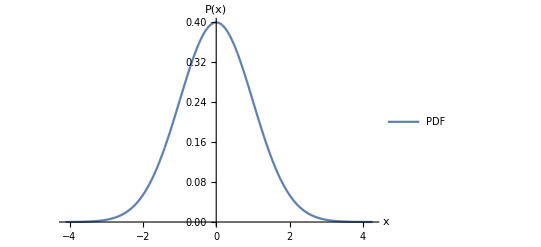

```mathematica
ListLinePlot[pdfNormal,PlotLegends->{"PDF"},AxesLabel->{"x","P(x)"},LabelStyle->Directive[Black,16]]
```

#### Shift in the mean

```mathematica
dp=0.00001;
CDFList=Table[{z+1,p},{p,dp,1-dp,dp}];
pdfShiftMean=Transpose[{CDFList[[2;;All,1]],Differences[CDFList[[All,2]]]/Differences[CDFList[[All,1]]]}];
```

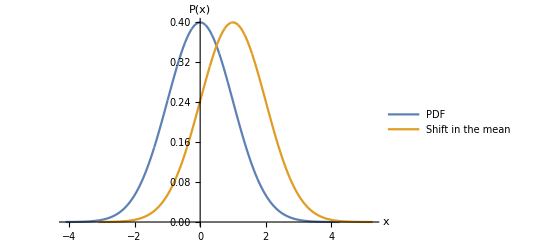

```mathematica
ListLinePlot[{pdfNormal,pdfShiftMean},PlotLegends->{"PDF","Shift in the mean"},AxesLabel->{"x","P(x)"},LabelStyle->Directive[Black,16]]
```

#### Shift in variance

```mathematica
dp=0.00001;
CDFList=Table[{z+z/2,p},{p,dp,1-dp,dp}];
pdfShiftVariance=Transpose[{CDFList[[2;;All,1]],Differences[CDFList[[All,2]]]/Differences[CDFList[[All,1]]]}];
```

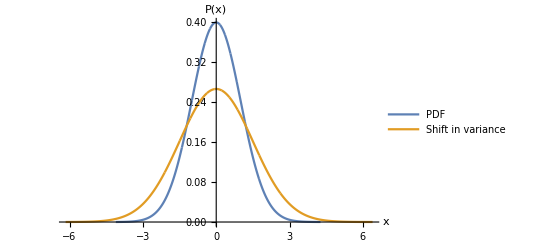

```mathematica
ListLinePlot[{pdfNormal,pdfShiftVariance},PlotLegends->{"PDF","Shift in variance"},AxesLabel->{"x","P(x)"},LabelStyle->Directive[Black,16]]
```

#### Shift in skewness

Notice here that = 0.7 and not 1 as in the other cases. If equal to 1 you will start seeing some singularities for very very low quantiles (lower than p = 0.001). This is a consequence of the expansion being less valid for higher values of skewness.

```mathematica
dp=0.00001;
CDFList=Table[{z+0.7(z^(2)-1)/6,p},{p,dp,1-dp,dp}];
pdfShiftSkewness=Transpose[{CDFList[[2;;All,1]],Differences[CDFList[[All,2]]]/Differences[CDFList[[All,1]]]}];
```

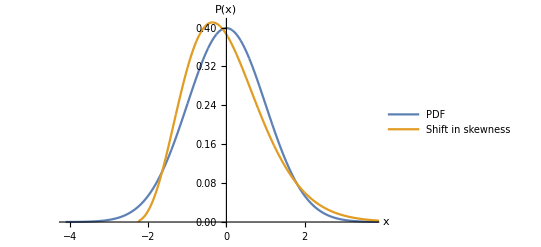

```mathematica
ListLinePlot[{pdfNormal,pdfShiftSkewness},PlotLegends->{"PDF","Shift in skewness"},AxesLabel->{"x","P(x)"},LabelStyle->Directive[Black,16]]
```

#### Shift in kurtosis

```mathematica
dp=0.00001;
CDFList=Table[{z+3(z^(3)-3z)/24,p},{p,dp,1-dp,dp}];
pdfShiftKurtosis=Transpose[{CDFList[[2;;All,1]],Differences[CDFList[[All,2]]]/Differences[CDFList[[All,1]]]}];
```

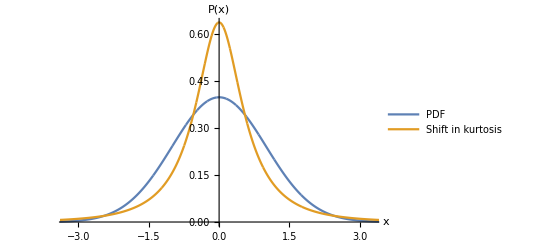

```mathematica
ListLinePlot[{pdfNormal,pdfShiftKurtosis},PlotLegends->{"PDF","Shift in kurtosis"},AxesLabel->{"x","P(x)"},LabelStyle->Directive[Black,16]]
```